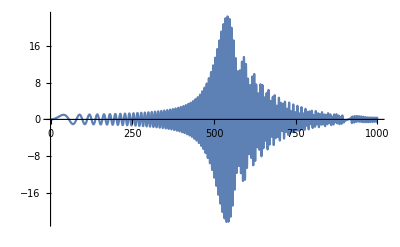

```mathematica
tmax=1000;
tmin=0;
x0=0;
v0=0;
rule=NDSolve[{x''[t]+0.02x'[t]+x[t]==Sin[0.001 t^2],x[0]==x0,x'[0]==v0},x[t],{t,tmin,tmax}];
Plot[x[t]/.rule,{t,tmin,tmax},PlotRange->All]
```

```mathematica
DSolve[x''[t]+0.02x'[t]+x[t]==Sin[0.001 t^2],x[t],t]
```

{{x[t]→ⅇ^(-0.01 t) C[2] Cos[0.99995 t]+ⅇ^(-0.01 t) C[1] Sin[0.99995 t]-(580.137+862.688 ⅈ) ⅇ^(-0.01 t) ((1.+0. ⅈ) Cos[0.99995 t] Erf[(11.2916+11.068 ⅈ)-(0.0223607+0.0223607 ⅈ) t]+(0.0000454226-1.38466×10^-20 ⅈ) Cos[0.99995 t] Erf[(11.068+11.2916 ⅈ)+(0.0223607+0.0223607 ⅈ) t]-(0.926133-0.377197 ⅈ) Cos[0.99995 t] Erfi[(11.068+11.2916 ⅈ)-(0.0223607+0.0223607 ⅈ) t]-(0.0000420674-0.0000171333 ⅈ) Cos[0.99995 t] Erfi[(11.2916+11.068 ⅈ)+(0.0223607+0.0223607 ⅈ) t]-(0.+1. ⅈ) Erf[(11.2916+11.068 ⅈ)-(0.0223607+0.0223607 ⅈ) t] Sin[0.99995 t]+(1.38466×10^-20+0.0000454226 ⅈ) Erf[(11.068+11.2916 ⅈ)+(0.0223607+0.0223607 ⅈ) t] Sin[0.99995 t]-(0.377197+0.926133 ⅈ) Erfi[(11.068+11.2916 ⅈ)-(0.0223607+0.0223607 ⅈ) t] Sin[0.99995 t]+(0.0000171333+0.0000420674 ⅈ) Erfi[(11.2916+11.068 ⅈ)+(0.0223607+0.0223607 ⅈ) t] Sin[0.99995 t])}}